```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["FunctionApproximations`"];
```

```mathematica
(*Discovered*)
```

```mathematica
eqn=0.962725940889723*u'[t]*u[t]-0.018285902991910394*u''[t]-0.0013675991131973635==u'[t]
```

-0.0013676+0.962726 u[t] u'[t]-0.0182859 u''[t]==u'[t]

```mathematica
sol=u[t]/.First@NDSolve[{eqn,u[0]==0,u'[0]==5.77},{u[t]},{t,0,1},Method->{"StiffnessSwitching","NonstiffTest"->Automatic}]
```

InterpolatingFunction[…][t]

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\user\Documents\GitHub\optics_R_exp\optics_data

```mathematica
gridfilename=StringJoin["grid_",ToString[0.1],".csv"];
rfilename=StringJoin["R_",ToString[0.1],".csv"];
x=Import[gridfilename];
x1=N[x/Max[x]];
y=Import[rfilename];
x1=Flatten[x1];
y1=Flatten[y];
data=Transpose[{x1,y1}];
```

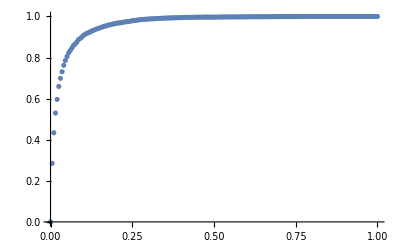

```mathematica
p1=ListPlot[data,PlotRange->All]
```

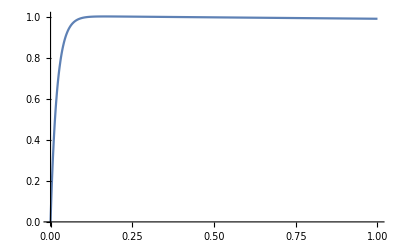

```mathematica
p2=Plot[9*sol,{t,0,1},PlotRange->All]
```

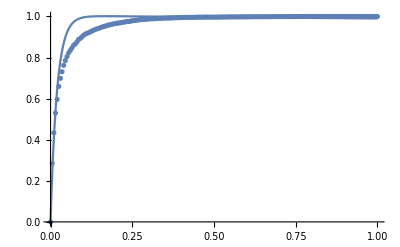

```mathematica
Show[p1,p2]
```

```mathematica
(*Sparse regression*)
```

```mathematica
coeffs={-1.18329356,-0.07453643,4.16046779,1,-4.12369603,-0.08368092}
```

{-1.18329,-0.0745364,4.16047,1,-4.1237,-0.0836809}

```mathematica
terms={u'[t]*u[t],u''[t],1,u'[t],u[t],u[t]*u''[t]}
```

{u[t] u'[t],u''[t],1,u'[t],u[t],u[t] u''[t]}

```mathematica
eqn2=coeffs.terms==0
```

4.16047-4.1237 u[t]+u'[t]-1.18329 u[t] u'[t]-0.0745364 u''[t]-0.0836809 u[t] u''[t]==0

```mathematica
sol2=u[t]/.First@NDSolve[{eqn2,u[0]==0,u'[0]==1000},{u[t]},{t,0,1},Method->{"StiffnessSwitching","NonstiffTest"->Automatic}]
```

InterpolatingFunction[…][t]

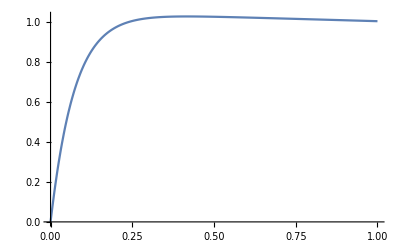

```mathematica
p3=Plot[8/600*sol2,{t,0,1},PlotRange->All]
```

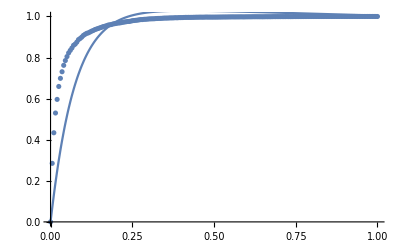

```mathematica
Show[p1,p3]
```